```mathematica
RegulaFalsiWI[x0_,x1_,n_,f_]:=
Module[{xk,xk1,xk2},xk=N[x0];xk1=N[x1];
If[f[xk]*f[xk1]>0,
Print["We cannot continue with Regula Falsi Method as function values are not of opposite sign at end points of intervals"];Return[]];
i=1;
output={};
While[i≤n,xk2=(xk*f[xk1]-xk1*f[xk])/(f[xk1]-f[xk]);
interval="["<>ToString[NumberForm[xk,12]]<>", "<>ToString[NumberForm[xk1,12]]<>"]";
output=Append[output,{i,interval,xk2,f[xk2]}];
If[Sign[f[xk1]]==Sign[f[xk2]],xk1=xk2,xk=xk2];i++;];
Print[NumberForm[TableForm[output,TableHeadings->{None,{"i","Interval","xi","f[xi]"}}],8]];
Print["Root after ",n," iterations = ",NumberForm[xk2,8]];
Print["Function value at approximated root, f[xi] = ",NumberForm[f[xk2],8]];];
Question 1
g[x_]:= x^3-5x+1;
RegulaFalsiWI[-1,1,10,g]
```

Question

i | Interval | xi | f[xi]
1 | [-1., 1.] | 0.25 | -0.234375
2 | [-1., 0.25] | 0.19402985 | 0.037155501
3 | [0.194029850746, 0.25] | 0.20168865 | -0.00023892045
4 | [0.194029850746, 0.201688654959] | 0.20163972 | -2.2244344×10^-7
5 | [0.194029850746, 0.201639721325] | 0.20163968 | -2.0708324×10^-10
6 | [0.194029850746, 0.201639675766] | 0.20163968 | -1.9273472×10^-13
7 | [0.194029850746, 0.201639675723] | 0.20163968 | -4.4408921×10^-16
8 | [0.194029850746, 0.201639675723] | 0.20163968 | 1.110223×10^-16
9 | [0.201639675723, 0.201639675723] | 0.20163968 | 1.110223×10^-16
10 | [0.201639675723, 0.201639675723] | 0.20163968 | -2.220446×10^-16

Root after 10 iterations = 0.20163968

Function value at approximated root, f[xi] = -2.220446×10^-16

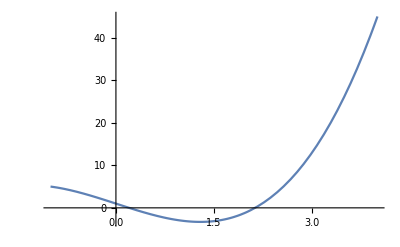

```mathematica
Plot[g[x],{x,-1,4}]
```

```mathematica
Question 2
```

```mathematica
g[x_]:=Cos[x]-x*Exp[x]
RegulaFalsiWI[0,1,8,g]
```

i | Interval | xi | f[xi]
1 | [0., 1.] | 0.31466534 | 0.51987117
2 | [0.314665337801, 1.] | 0.44672814 | 0.20354478
3 | [0.446728144591, 1.] | 0.49401534 | 0.070802349
4 | [0.494015336596, 1.] | 0.50994614 | 0.023607719
5 | [0.509946140365, 1.] | 0.51520101 | 0.0077601137
6 | [0.515201009902, 1.] | 0.51692221 | 0.0025388647
7 | [0.516922210011, 1.] | 0.51748468 | 0.00082935789
8 | [0.517484676785, 1.] | 0.51766834 | 0.00027078573

Root after 8 iterations = 0.51766834

Function value at approximated root, f[xi] = 0.00027078573

```mathematica
Question 3
g[x_]:=x^4-3x^2+x-10;
RegulaFalsiWI[2,3,7,g]
```

3 Question

i | Interval | xi | f[xi]
1 | [2., 3.] | 2.0784314 | -2.2198625
2 | [2.07843137255, 3.] | 2.119995 | -1.1637008
3 | [2.11999499205, 3.] | 2.1412571 | -0.59162874
4 | [2.14125711528, 3.] | 2.1519325 | -0.29607559
5 | [2.15193245843, 3.] | 2.1572414 | -0.1469951
6 | [2.15724139986, 3.] | 2.159869 | -0.072691406
7 | [2.15986895617, 3.] | 2.1611663 | -0.035876602

Root after 7 iterations = 2.1611663

Function value at approximated root, f[xi] = -0.035876602